## Estimation of Coupled Exponential Distribution

### Plot of equations of GeoMean, mean of pairs, second moment of triplets.

From notes by Amaneh Al-Najafi

Correction: the equation for G (geometric mean), the sign of κ needs to be reversed. This changes the equation to reference from the paper by Vogel to:
G = (σ μ)/κ Exp[PolyGamma[1]-PolyGamma[1+1/κ]+κ]

The results below are based on Amenah’s derivation; however, the Mathematica derivation showed  a difference, so this section will eventually be modified.

```mathematica
$Assumptions=={μ,σ,κ}∈Reals&&0<σ<∞&&0<κ<∞&&0<=p<=1
```

True=={μ,σ,κ}∈ℝ&&0<σ<∞&&0<κ<∞&&0≤p≤1

```mathematica
Clear[CoupledExponentialEstimators,GeoMean,MeanPairs,SecondMomentTriplets];
CoupledExponentialEstimators[GeoMean_,MeanPairs_,SecondMomentTriplets_]:=
{
GeoMean==(σ μ)/κ Exp[PolyGamma[1]-PolyGamma[1+1/κ]+κ],
MeanPairs==μ+σ/2,
SecondMomentTriplets==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}
```

```mathematica
ContourPlot3D[Evaluate@CoupledExponentialEstimators[2.72,2.25,0.424],
{μ,0,4},{σ,0,2},{κ,0,3},
AxesLabel->{μ,σ,κ},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}]
```

-Graphics3D-

```mathematica
ContourPlot3D[Evaluate@CoupledExponentialEstimators[3.17,2.25,4.15],
{μ,0,4},{σ,0,2},{κ,0,3},
AxesLabel->{μ,σ,κ},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}]
```

-Graphics3D-

```mathematica
ContourPlot3D[Evaluate@CoupledExponentialEstimators[4.98,2.25,5589],
{μ,0,4},{σ,0,2},{κ,0,3},
AxesLabel->{μ,σ,κ},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}]
```

-Graphics3D-

### Derivation of the GeoMean of the Coupled Exponential Distribution

#### Assuming μ = 0

The Quantile function of the Coupled Exponential Distribution
If[κ!=0,-σ/κ(1-(1-p)^-κ),
-σ Log[1-p]
]
simplifies to σ CoupledLogarithm[(1-p)^-1,κ]

```mathematica
ClearAll[p,κ];
```

```mathematica
ClearAll[CoupledExponentialQuantileFunction];
CoupledExponentialQuantileFunction[p_,μ_:0,σ_,κ_]:=
CoupledExponentialQuantileFunction[p,μ,σ,κ]=σCoupledLogarithm[(1-p)^-1,κ,0]
```

Test Quantile Function

```mathematica
CoupledExponentialQuantileFunction[0.999,0,1,-0.5]
```

1.93675

```mathematica
If[κ!=0,-σ/κ(1-(1-p)^-κ),
-σ Log[1-p]
]/.{p->0.999,σ->1,κ->-0.5}
```

1.93675

Integration of Quantile Function to form Geometric Mean

```mathematica
FullSimplify@Exp[∫_0^1 FullSimplify@Log@CoupledExponentialQuantileFunction[p,0,σ,κ]ⅆp]
```

ⅇ^(∫_0^1 ConditionalExpression[Piecewise[{{Log[((-1+(1-p)^-κ) σ)/κ], κ≠0}, {Log[-σ Log[1-p]], True}}], p<1]ⅆp)

```mathematica
Assuming[0<κ<∞,FullSimplify@Exp[∫_0^1 FullSimplify@Log[((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

(ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ

```mathematica
Assuming[-1<κ<0,FullSimplify@Exp[∫_0^1 FullSimplify@Log[((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) σ)/κ

```mathematica
FullSimplify@Exp[∫_0^1 Log[- σ Log[1-p]]ⅆp]
```

ⅇ^-EulerGamma σ

The Harmonic number and the Digamma functions have the following relationship. 
H_z=ψ(z+1)-γ where γ is the Euler gamma constant 0.5172216...

See this Wolfram Research article on the history.
https://functions.wolfram.com/GammaBetaErf/HarmonicNumber2/introductions/DifferentiatedGammas/ShowAll.html

Summarizing Result

GeometricMean of Coupled Exponential =
Piecewise[{{(ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ, κ>0}, {-(ⅇ^(κ-HarmonicNumber[-(1+κ)/κ]) σ)/κ, -1<κ<0}, {ⅇ^-EulerGamma σ, κ=0}}]

#### Assuming μ ≠ 0

```mathematica
ClearAll[CoupledExponentialQuantileFunction];
CoupledExponentialQuantileFunction[p_,μ_,σ_,κ_]:=
CoupledExponentialQuantileFunction[p,μ,σ,κ]=μ+σCoupledLogarithm[(1-p)^-1,κ,0]
```

```mathematica
Assuming[0<κ<∞&&μ∈Reals,FullSimplify@Exp[∫_0^1 FullSimplify@Log[μ+((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

ConditionalExpression[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0]

```mathematica
Assuming[-1<κ<0&&μ∈Reals,FullSimplify@Exp[∫_0^1 FullSimplify@Log[μ+((-1+(1-p)^-κ) σ)/κ]ⅆp]]
```

ConditionalExpression[ⅇ^(-π (-1+(κ μ)/σ)^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0]

```mathematica
Assuming[μ∈Reals,FullSimplify@Exp[∫_0^1 Log[μ- σ Log[1-p]]ⅆp]]
```

$Aborted

Check relationship with equation solved by Amenah

```mathematica
FullSimplify[(μ σ)/κ Exp[PolyGamma[1]-PolyGamma[1+1/κ]],0<κ<∞&&0<=μ<∞&&0<σ<∞]
```

(ⅇ^(-HarmonicNumber[1/κ]) μ σ)/κ

```mathematica
FullSimplify[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]),0<κ<∞]
```

ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])

```mathematica
FullSimplify[Limit[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])μ,μ->0],0<κ<∞]
```

(ⅇ^(-HarmonicNumber[-1+1/κ]) σ)/κ

```mathematica
FullSimplify[Limit[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ])μ,κ->0],μ>=0]
```

lim_(κ→0) ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ

Summarizing Result

GeometricMean of Coupled Exponential =
Piecewise[{{ConditionalExpression[ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0], κ>0}, {ConditionalExpression[ⅇ^(-π (-1+(κ μ)/σ)^(-1/κ) Csc[π/κ]+κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ, μ≥0], -1<κ<0}, {?, κ=0}}]

### Reduction of Equations

```mathematica
Solve[
{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
MeanPairs==μ+σ/2,
SecondMomentTriplets==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
},{μ,σ,κ},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,MeanPairs==μ+σ/2,SecondMomentTriplets==μ^2+(2 μ σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},{μ,σ,κ},ℝ]

Fix mistake in next equation

```mathematica
μ==MeanPairs-σ/2
```

```mathematica
Solve[
{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),
SecondMomentTriplets==(MeanPairs-σ/2)^2+(2(MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3(3+κ))
},{σ,κ},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),SecondMomentTriplets==(MeanPairs-σ/2)^2+(2 (MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},{σ,κ},ℝ]

```mathematica
SolveValues[
{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),
SecondMomentTriplets==(MeanPairs-σ/2)^2+(2(MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3(3+κ))
},{σ,κ},Reals]
```

SolveValues::nsmet: This system cannot be solved with the methods available to SolveValues.

SolveValues[{GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),SecondMomentTriplets==(MeanPairs-σ/2)^2+(2 (MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},{σ,κ},ℝ]

```mathematica
SolveValues[
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),
σ,Reals]
```

SolveValues::nsmet: This system cannot be solved with the methods available to SolveValues.

SolveValues[GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-σ/2))/σ]) (MeanPairs-σ/2),σ,ℝ]

```mathematica
Solve[
SecondMomentTriplets==(MeanPairs-σ/2)^2+(2(MeanPairs-σ/2) σ)/(3+κ)+(2 σ^2)/(3(3+κ)),
σ,Reals]
```

```mathematica
{{σ->ConditionalExpression[(6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)), (SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2)&&κ>-5/3)||(-3<κ<-5/3&&SecondMomentTriplets<(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))||(κ<-3&&SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))]},{σ->ConditionalExpression[(6 (MeanPairs+MeanPairs κ))/(5+3 κ)+2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)), (SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2)&&κ>-5/3)||(-3<κ<-5/3&&SecondMomentTriplets<(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))||(κ<-3&&SecondMomentTriplets>(12 MeanPairs^2+8 MeanPairs^2 κ)/(15+14 κ+3 κ^2))]}}
```

Simplify expression in terms of κ

```mathematica
FullSimplify[GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (MeanPairs-((6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)))/2))/((6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2)))]) (MeanPairs-1/2((6 (MeanPairs+MeanPairs κ))/(5+3 κ)-2 √3 √(1/(5+3 κ)^2(-12 MeanPairs^2+15 SecondMomentTriplets-8 MeanPairs^2 κ+14 SecondMomentTriplets κ+3 SecondMomentTriplets κ^2))))]
```

1/(5+3 κ)ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,(-2 MeanPairs (3+2 κ)+(2+κ) (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))/(-6 MeanPairs (1+κ)+2 (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))]) (2 MeanPairs+(5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))==GeoMean

### Contour Plots

```mathematica
Manipulate[
ContourPlot3D[
1/(5+3 κ)ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,(-2 MeanPairs (3+2 κ)+(2+κ) (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))/(-6 MeanPairs (1+κ)+2 (5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))]) (2 MeanPairs+(5+3 κ) √(SecondMomentTriplets+(4 MeanPairs^2)/(5+3 κ)^2+(4 (-2 MeanPairs^2+SecondMomentTriplets))/(5+3 κ)))==GeoMean,
{GeoMean,0,5},{MeanPairs,0,5},{SecondMomentTriplets,0,5},
AxesLabel->{"MeanPairs","SecondMomentTriplets","GeoMean"}],
{{κ,1},0,2}
]
```

```mathematica
Manipulate[
ContourPlot3D[
Evaluate[{
GeoMean==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
MeanPairs==μ+σ/2,
SecondMomentTriplets==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{GeoMean,0,5},{MeanPairs,0,5},{SecondMomentTriplets,0,5},
AxesLabel->{"GeoMean","MeanPairs","SecondMomentTriplets"},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}],
{{μ,0.1},0,2},{{σ,1},0,10},{{κ,0.5},0,2}
]
```

#### Contour Plots for distribution parameters given moment estimations

Attempts to use the Manipulate control result in aborted computation

```mathematica
Manipulate[
ContourPlot3D[
Evaluate[{
ⅇ^(κS Hypergeometric2F1[1,1/κS,1+1/κS,1-(κS μS)/σS]) μS==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
μS+σS/2==μ+σ/2,
μS^2+(2μS σS)/(3+κS)+(2 σS^2)/(3(3+κS))==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{μ,0,4},{σ,0,1.1},{κ,0,2},
AxesLabel->{"μ","σ","κ"},
PlotLegends->{"GeoMean","MeanPairs","SecondMomentTriplets"}],
{{μS,0.1},0,5},{{σS,1},0,10},{{κS,0.5},0,2}
]
```

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

First compute a set of moments

```mathematica
Manipulate[
Evaluate[{
ⅇ^(κS Hypergeometric2F1[1,1/κS,1+1/κS,1-(κS μS)/σS]) μS==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,
μS+σS/2==μ+σ/2,
μS^2+(2μS σS)/(3+κS)+(2 σS^2)/(3(3+κS))==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{{μS,0.1},0,5},{{σS,1},0,10},{{κS,0.5},0,2}
]
```

Try Contour Maps from simplest to hardest curve individually

```mathematica
CEEstimationPlot[Equation_,EquationLabel_]:=ContourPlot3D[
Evaluate[Equation],
{μ,0,4},{σ,0,1.1},{κ,0,2},
AxesLabel->{"μ","σ","κ"},
PlotLegends->{EquationLabel},
PlotLabel->"μ=2, σ=3, κ=1"]
```

```mathematica
CEEstimationPlot[7/2==μ+σ/2,"MeanPairs"]
```

-Graphics3D-

```mathematica
CEEstimationPlot[17/2==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ)),"SecondMomentTriplets"]
```

-Graphics3D-

```mathematica
CEEstimationPlot[27/4==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ μ)/σ]) μ,"GeoMean"]
```

General::munfl: 0.1375^6999999 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.94477×10^-301)/-335997648 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(4.85853×10^-307)/342997550 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

Not sure why the 3D contour plot for the MeanPair and SecondMomentTriplets does not show an intersection but presumably it has something to do with the internal contour parameter settings

```mathematica
ContourPlot3D[
Evaluate[{
7/2==μ+σ/2,
17/2==μ^2+(2μ σ)/(3+κ)+(2 σ^2)/(3(3+κ))
}],
{μ,0,4},{σ,0,1.1},{κ,0,2},
AxesLabel->{"μ","σ","κ"},
PlotLegends->{"MeanPairs","SecondMomentTriplets"},
PlotLabel->"μ=2, σ=3, κ=1"]
```

-Graphics3D-

2D Plots do show clear intersections

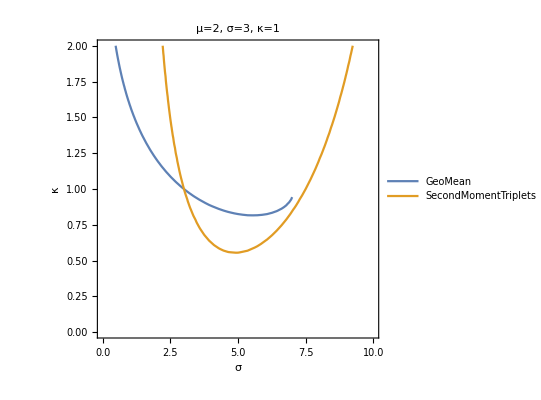

```mathematica
ContourPlot[{27/4==ⅇ^(κ Hypergeometric2F1[1,1/κ,1+1/κ,1-(κ (7/2-σ/2))/σ]) (7/2-σ/2),17/2==(7/2-σ/2)^2+(2 (7/2-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ))},
{σ,0,10},{κ,0,2},
FrameLabel->{"σ","κ"},
PlotLegends->{"GeoMean","SecondMomentTriplets"},
PlotLabel->"μ=2, σ=3, κ=1"]
```

#### Saved Plots

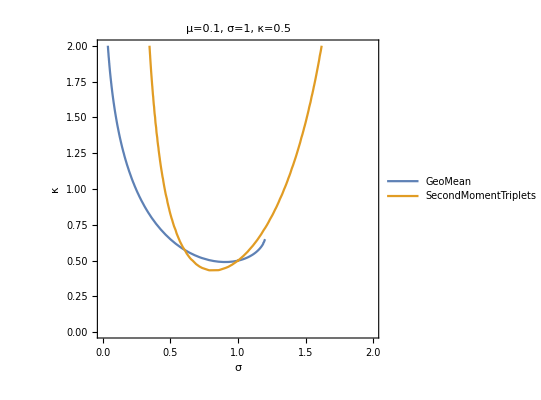

-Graphics-

Find Minimum of SecondMomentTriples with respect to κ

```mathematica
Solve[17/2==(7/2-σ/2)^2+(2 (7/2-σ/2) σ)/(3+κ)+(2 σ^2)/(3 (3+κ)),κ]
```

{{κ→(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2))}}

```mathematica
FindMinimum[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,1}]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{-4.3368×10^14,{σ→1.16905}}

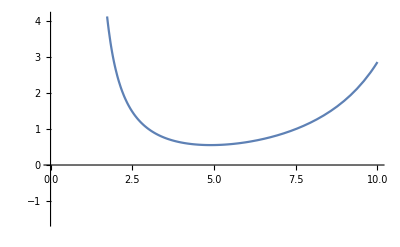

```mathematica
Plot[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,0,10}, PlotRange->Automatic]
```

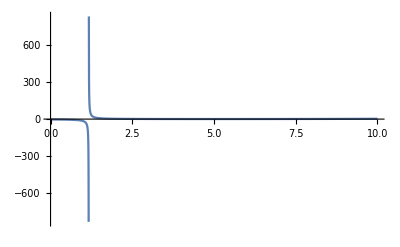

```mathematica
Plot[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,0,10}, PlotRange->Full]
```

```mathematica
FindMinimum[(-135+42 σ-5 σ^2)/(3 (15-14 σ+σ^2)),{σ,2}]
```

{0.554805,{σ→4.89929}}

So there are some challenges with the search for σ and κ if the search does not seed a value close to the solution. In particular the zero of (15-14 σ+σ^2) causes κ to go to infinity.  It’s important to be the side that produces a positive kappa